```mathematica
link=LinkConnect["8000",LinkProtocol->"TCPIP",LinkHost->"134.169.81.78",LinkOptions->4];
If[LinkReadyQ[link],LinkRead[link]]
```

Hello client program.

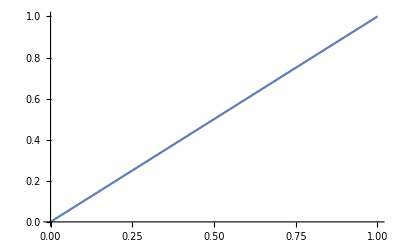

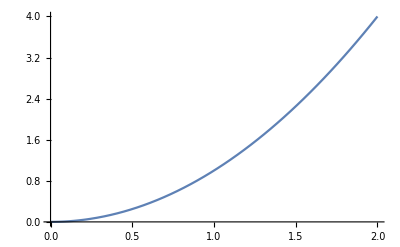

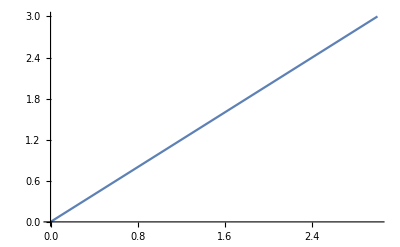

{0.9,1.9,2.9,3.9,4.9,5.9,6.9,7.9,8.9,9.9,10.9,11.9,12.9,13.9,14.9,15.9,16.9,17.9,18.9,19.9}

```mathematica
Do[If[LinkReadyQ[link],Print[LinkRead[link]],LinkWrite[link, "End"];Break[]],20]
```

```mathematica
list
```

{0.9,1.9,2.9,3.9,4.9,5.9,6.9,7.9,8.9,9.9,10.9,11.9,12.9,13.9,14.9,15.9,16.9,17.9,18.9,19.9}

```mathematica
Plus[1,3]
```

4

```mathematica
Set[a,1]
```

1

```mathematica
a
```

1